```mathematica
fϕθ=Sin[θ]^2(3+(Cos[θ]^2-Sin[θ]^2) - 2 (Cos[ϕ]^2-Sin[ϕ]^2)Sin[θ]^2)/16
%/.{Cos[θ]->z,Sin[θ]->Sqrt[(1-z^2)],Cos[ϕ]->x/Sqrt[(1-z^2)],Sin[ϕ]->y/Sqrt[(1-z^2)]};
FullSimplify[%];
FullSimplify[%,Assumptions->x^2+y^2+z^2==1]
```

1/16 Sin[θ]^2 (3+Cos[θ]^2-Sin[θ]^2-2 Sin[θ]^2 (Cos[ϕ]^2-Sin[ϕ]^2))

-1/4 (-1+z^2) (y^2+z^2)

```mathematica
D[Sqrt[Sin[θ]^2(1-Cos[ϕ]^2Sin[θ]^2)/4],ϕ]/.{ϕ->90*(2 Pi/360),θ-> 90*(2Pi/360)}
D[Sqrt[Sin[θ]^2(1-Cos[ϕ]^2Sin[θ]^2)/4],θ]/.{ϕ->90*(2 Pi/360),θ-> 90*(2Pi/360)}
D[Sqrt[Sin[θ]^2(1-Cos[ϕ]^2Sin[θ]^2)/4],ϕ]/.{ϕ->180*(2 Pi/360),θ-> 45*(2Pi/360)}
D[Sqrt[Sin[θ]^2(1-Cos[ϕ]^2Sin[θ]^2)/4],θ]/.{ϕ->180*(2 Pi/360),θ-> 45*(2Pi/360)}
```

0

0

0

«1 more identical outputs»

```mathematica
LittleH[d_,e_,β_,δ_]=blockHamiltonian[[23]];
%//MatrixForm
EpParallel[β_,δ_]=FullSimplify[(Eigenvalues[LittleH[d,e,β,δ]/.{ϕ->0,θ->0}]-HTest[0,0,β,δ][[7]][[7]])/.{d->0.1,e->-0.1/4}][[2]];
EmParallel[β_,δ_] =FullSimplify[(Eigenvalues[LittleH[d,e,β,δ]/.{ϕ->0,θ->0}]-HTest[0,0,β,δ][[7]][[7]])/.{d->0.1,e->-0.1/4}][[1]];
EpBent[β_,δ_]=FullSimplify[(Eigenvalues[LittleH[d,e,β,δ]/.{ϕ->Pi/2,θ->Pi/2}]-HTest[Pi/2,Pi/2,β,δ][[7]][[7]])/.{d->0.1,e->-0.1/4}][[2]];
EmBent[β_,δ_] =FullSimplify[(Eigenvalues[LittleH[d,e,β,δ]/.{ϕ->Pi/2,θ->Pi/2}]-HTest[Pi/2,Pi/2,β,δ][[7]][[7]])/.{d->0.1,e->-0.1/4}][[1]];
Ep=FullSimplify[(Eigenvalues[LittleH[d,e,β,δ]])][[2]]
Em=FullSimplify[(Eigenvalues[LittleH[d,e,β,δ]])][[1]]
```

(1-δ+1/48 ((-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])-6 (d+3 e+(d-e) Cos[β]) Cos[2 ϕ] Sin[θ]^2) | -1/2 (d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ])
-1/2 (d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]-ⅈ Sin[ϕ]) | -1+δ+1/48 ((-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])-6 (d+3 e+(d-e) Cos[β]) Cos[2 ϕ] Sin[θ]^2))

1/48 (d (-1+3 Cos[β]) (1+3 Cos[2 θ])+6 e (-3+Cos[β]) Cos[2 ϕ] Sin[θ]^2-6 Cos[β/2]^2 (e+3 e Cos[2 θ]+2 d Cos[2 ϕ] Sin[θ]^2)+3 √(10 (d-e)^2+256 (-1+δ)^2-2 (d-e)^2 (2 Cos[4 θ] Cos[ϕ]^2+4 Cos[2 β] (3+Cos[2 θ]) Sin[θ]^2+Cos[2 ϕ] (3-8 Cos[2 β] Sin[θ]^4)+8 Cos[2 θ] Sin[ϕ]^2)))

1/48 (d (-1+3 Cos[β]) (1+3 Cos[2 θ])+6 e (-3+Cos[β]) Cos[2 ϕ] Sin[θ]^2-6 Cos[β/2]^2 (e+3 e Cos[2 θ]+2 d Cos[2 ϕ] Sin[θ]^2)-3 √(10 (d-e)^2+256 (-1+δ)^2-2 (d-e)^2 (2 Cos[4 θ] Cos[ϕ]^2+4 Cos[2 β] (3+Cos[2 θ]) Sin[θ]^2+Cos[2 ϕ] (3-8 Cos[2 β] Sin[θ]^4)+8 Cos[2 θ] Sin[ϕ]^2)))

```mathematica
Eigensystem[LittleH[d,e,β,δ]/.{ϕ->Pi/2,θ->Pi/2}]/.{d->0.1,e->-0.1/3}//MatrixForm
Eigensystem[LittleH[d,e,β,δ]/.{ϕ->Pi/2,θ->Pi/2}]/.{d->0.1,e->-0.1/4}//MatrixForm
```

(1/12 (0.-3 √2 √(8.01778-16 δ+8 δ^2-0.0177778 Cos[2 β])) | 1/12 (0.+3 √2 √(8.01778-16 δ+8 δ^2-0.0177778 Cos[2 β]))
{(0.+3.75 ⅈ) (-4+4 δ+√2 √(8.01778-16 δ+8 δ^2-0.0177778 Cos[2 β])) Csc[β],1} | {(0.-3.75 ⅈ) (4-4 δ+√2 √(8.01778-16 δ+8 δ^2-0.0177778 Cos[2 β])) Csc[β],1})

(1/12 (0.05-3 √2 √(8.01563-16 δ+8 δ^2-0.015625 Cos[2 β])) | 1/12 (0.05+3 √2 √(8.01563-16 δ+8 δ^2-0.015625 Cos[2 β]))
{(0.+4. ⅈ) (-4+4 δ+√2 √(8.01563-16 δ+8 δ^2-0.015625 Cos[2 β])) Csc[β],1} | {(0.-4. ⅈ) (4-4 δ+√2 √(8.01563-16 δ+8 δ^2-0.015625 Cos[2 β])) Csc[β],1})

```mathematica
EpBentList=Re[Table[EpBent[β,δ],{δ,0.9,1.1,0.01},{β,0,Pi,0.01}]];
EmBentList=Re[Table[EmBent[β,δ],{δ,0.9,1.1,0.01},{β,0,Pi,0.01}]];
ListPlot3D[{EpBentList,EmBentList}]
```

-Graphics3D-

```mathematica
ListPlot3D[EmBentList-Table[HTest[Pi/2,Pi/2,β,δ][[7]][[7]]/.{d->0.1,e->-0.1/4},{δ,0.9,1.1,0.01},{β,0,Pi,0.01}]]
ListPlot3D[EpBentList-Table[HTest[Pi/2,Pi/2,β,δ][[7]][[7]]/.{d->0.1,e->-0.1/4},{δ,0.9,1.1,0.01},{β,0,Pi,0.01}]]
ListPlot3D[EpBentList-EmBentList]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Export["/Users/sina/Google Drive/Research/Singlet Fission Project/21_1n1_Analysis/Data Files/21_1n1_avoidedCrossing_3Ddata_Bparallely_Ep.txt",Transpose[EpBentList],"Table"];
Export["/Users/sina/Google Drive/Research/Singlet Fission Project/21_1n1_Analysis/Data Files/21_1n1_avoidedCrossing_3Ddata_Bparallely_Em.txt",Transpose[EmBentList],"Table"];
```

```mathematica
EpParallelList=Table[EpParallel[β,δ],{δ,0.9,1.1,0.01},{β,0,Pi,0.01}];
EmParallelList=Table[EmParallel[β,δ],{δ,0.9,1.1,0.01},{β,0,Pi,0.01}];
ListPlot3D[{EpParallelList,EmParallelList}]
```

-Graphics3D-

```mathematica
Export["/Users/sina/Google Drive/Research/Singlet Fission Project/21_1n1_Analysis/Data Files/21_1n1_avoidedCrossing_3Ddata_Bparallelz_Ep.txt",Transpose[EpParallelList],"Table"];
Export["/Users/sina/Google Drive/Research/Singlet Fission Project/21_1n1_Analysis/Data Files/21_1n1_avoidedCrossing_3Ddata_Bparallelz_Em.txt",Transpose[EmParallelList],"Table"];
```

```mathematica
U=Transpose[{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,ⅈ/Sqrt[2],1/Sqrt[2],0,0,0,0},{0,0,0,-ⅈ/Sqrt[2],1/Sqrt[2],0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1}}];
%//MatrixForm
FullSimplify[Chop[Transpose[U].HTest[0,0,0,0.7].U/.{d->0.1,e->0}]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/(√2) | -ⅈ/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(√2) | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(2 | 0 | 0 | 0.0408248 | 0.0408248 | 0 | -0.0471405 | 0 | 0.057735
0 | 1.71667 | 0 | 0.-0.0353553 ⅈ | 0.+0.0353553 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0.966667 | 0 | 0 | 0 | 0 | 0 | 0
0.0408248 | 0.-0.0353553 ⅈ | 0 | 0.025 | 0.341667 | 0 | 0.0288675 | 0 | 0
0.0408248 | 0.+0.0353553 ⅈ | 0 | 0.341667 | 0.025 | 0 | 0.0288675 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.283333 | 0 | 0.05 | 0
-0.0471405 | 0 | 0 | 0.0288675 | 0.0288675 | 0 | -0.966667 | 0 | 0.0408248
0 | 0 | 0 | 0 | 0 | 0.05 | 0 | -1.68333 | 0
0.057735 | 0 | 0 | 0 | 0 | 0 | 0.0408248 | 0 | -2.43333)

```mathematica
Abs[{0,0,0,0,0,0,1,0,0}.(sAx+sBx).{0,0,0,ⅈ/Sqrt[2],0,1/Sqrt[2],0,0,0}]^2
```

1/4

```mathematica
Abs[{0,0,0,0,0,0,1,0,0}.(sAy+sBy).{0,0,-ⅈ/Sqrt[2],0,1/Sqrt[2],0,0,0,0}]^2
```

0

```mathematica
Abs[HTest[ϕ,θ,Pi/2,δ][[1]][[7]]/.{d->0.1,e->-0.1/30}]^2
```

(ⅇ^(4 Im[ϕ]) Abs[0.36 ⅇ^(2 ⅈ ϕ) (1+3 Cos[2 θ])+1.08 Sin[θ]^2+1.08 ⅇ^(4 ⅈ ϕ) Sin[θ]^2]^2)/4608

```mathematica
FullSimplify[HTest[Pi/2,Pi/2,β,δ]/.{d->0.1,e->-0.1/3}]//MatrixForm
```

(2 | 0 | 0 | 0 | -0.07698 Cos[β] | 0 | 0. | 0 | -0.07698 Cos[β]
0 | 1.+δ | 0 | 0.0666667 Cos[β] | 0 | 0 | 0 | (0.-0.0666667 ⅈ) Sin[β] | 0
0 | 0 | 1. | 0 | (0.-0.0942809 ⅈ) Sin[β] | 0 | 0 | 0 | (0.-0.0942809 ⅈ) Sin[β]
0 | 0.0666667 Cos[β] | 0 | 1.-δ | 0 | (0.-0.0666667 ⅈ) Sin[β] | 0 | 0 | 0
-0.07698 Cos[β] | 0 | (0.+0.0942809 ⅈ) Sin[β] | 0 | -1.+2 δ | 0 | -0.0544331 Cos[β] | 0 | 0
0 | 0 | 0 | (0.+0.0666667 ⅈ) Sin[β] | 0 | -1.+δ | 0 | -0.0666667 Cos[β] | 0
0. | 0 | 0 | 0 | -0.0544331 Cos[β] | 0 | -1. | 0 | -0.0544331 Cos[β]
0 | (0.+0.0666667 ⅈ) Sin[β] | 0 | 0 | 0 | -0.0666667 Cos[β] | 0 | -1.-δ | 0
-0.07698 Cos[β] | 0 | (0.+0.0942809 ⅈ) Sin[β] | 0 | 0 | 0 | -0.0544331 Cos[β] | 0 | -1.-2 δ)

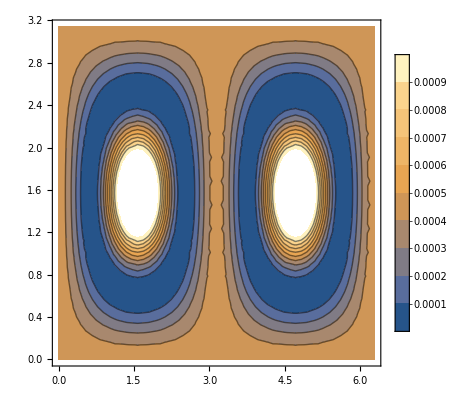

```mathematica
ContourPlot[Abs[HTest[ϕ,θ,Pi/2,δ][[1]][[7]]/.{d->0.1,e->-0.1/30}]^2,{ϕ,0,2Pi},{θ,0,Pi},PlotLegends->Automatic]//MatrixForm
```

```mathematica
HTest[Pi/2,Pi/2,β,δ]//MatrixForm
```

(2 | 0 | 0 | 0 | -(1/2 (d+3 e+(d-e) Cos[β])+1/2 (-d-3 e+3 (d-e) Cos[β]))/(2 √3) | 0 | -(24 (d+3 e+(d-e) Cos[β])-8 (-d-3 e+3 (d-e) Cos[β]))/(48 √2) | 0 | -(1/2 (d+3 e+(d-e) Cos[β])+1/2 (-d-3 e+3 (d-e) Cos[β]))/(2 √3)
0 | 1+δ+1/48 (6 (d+3 e+(d-e) Cos[β])-2 (-d-3 e+3 (d-e) Cos[β])) | 0 | 1/2 (d-e) Cos[β] | 0 | 0 | 0 | -1/2 ⅈ (d-e) Sin[β] | 0
0 | 0 | 1+1/3 (-d-3 e) | 0 | -(ⅈ (d-e) Sin[β])/(√2) | 0 | 0 | 0 | -(ⅈ (d-e) Sin[β])/(√2)
0 | 1/2 (d-e) Cos[β] | 0 | 1-δ+1/48 (6 (d+3 e+(d-e) Cos[β])-2 (-d-3 e+3 (d-e) Cos[β])) | 0 | -1/2 ⅈ (d-e) Sin[β] | 0 | 0 | 0
-(1/2 (d+3 e+(d-e) Cos[β])+1/2 (-d-3 e+3 (d-e) Cos[β]))/(2 √3) | 0 | (ⅈ (d-e) Sin[β])/(√2) | 0 | -1+1/3 (-d-3 e)+2 δ | 0 | -(1/2 (d+3 e+(d-e) Cos[β])+1/2 (-d-3 e+3 (d-e) Cos[β]))/(2 √6) | 0 | 0
0 | 0 | 0 | 1/2 ⅈ (d-e) Sin[β] | 0 | -1+δ+1/48 (6 (d+3 e+(d-e) Cos[β])-2 (-d-3 e+3 (d-e) Cos[β])) | 0 | 1/8 (-((d-e) Cos[β])+3 (-d+e) Cos[β]) | 0
-(24 (d+3 e+(d-e) Cos[β])-8 (-d-3 e+3 (d-e) Cos[β]))/(48 √2) | 0 | 0 | 0 | -(1/2 (d+3 e+(d-e) Cos[β])+1/2 (-d-3 e+3 (d-e) Cos[β]))/(2 √6) | 0 | -1+1/24 (6 (d+3 e+(d-e) Cos[β])-2 (-d-3 e+3 (d-e) Cos[β])) | 0 | -(1/2 (d+3 e+(d-e) Cos[β])+1/2 (-d-3 e+3 (d-e) Cos[β]))/(2 √6)
0 | 1/2 ⅈ (d-e) Sin[β] | 0 | 0 | 0 | 1/8 (-((d-e) Cos[β])+3 (-d+e) Cos[β]) | 0 | -1-δ+1/48 (6 (d+3 e+(d-e) Cos[β])-2 (-d-3 e+3 (d-e) Cos[β])) | 0
-(1/2 (d+3 e+(d-e) Cos[β])+1/2 (-d-3 e+3 (d-e) Cos[β]))/(2 √3) | 0 | (ⅈ (d-e) Sin[β])/(√2) | 0 | 0 | 0 | -(1/2 (d+3 e+(d-e) Cos[β])+1/2 (-d-3 e+3 (d-e) Cos[β]))/(2 √6) | 0 | -1+1/3 (-d-3 e)-2 δ)

```mathematica
ΔEpm[δ_]=FullSimplify[(Ep-Em),Assumptions->{β ∈ Reals,θ ∈ Reals,d>e,δ ∈ Reals,d ∈ Reals, e ∈ Reals}]/.{Cos[2θ]->Cos[θ]^2-Sin[θ]^2,Cos[2ϕ]->Cos[ϕ]^2-Sin[ϕ]^2,Cos[2β]->Cos[β]^2-Sin[β]^2,Cos[4θ]->TrigExpand[Cos[4θ]]}
ΔEpmAdd[δ_]=FullSimplify[(Ep+Em)-2HTest[ϕ,θ,β,δ][[7]][[7]],Assumptions->{β ∈ Reals,θ ∈ Reals,d>e,δ ∈ Reals,d ∈ Reals, e ∈ Reals}]/.{Cos[2θ]->Cos[θ]^2-Sin[θ]^2,Cos[2ϕ]->Cos[ϕ]^2-Sin[ϕ]^2,Cos[2β]->Cos[β]^2-Sin[β]^2,Cos[4θ]->TrigExpand[Cos[4θ]]}
ΔEp0[δ_]=FullSimplify[(Ep-HTest[ Pi/2,Pi/2,β,δ][[7]][[7]]),Assumptions->{β ∈ Reals,θ ∈ Reals,d>e,δ ∈ Reals,d ∈ Reals, e ∈ Reals}]/.{Cos[2θ]->Cos[θ]^2-Sin[θ]^2,Cos[2ϕ]->Cos[ϕ]^2-Sin[ϕ]^2,Cos[2β]->Cos[β]^2-Sin[β]^2,Cos[4θ]->TrigExpand[Cos[4θ]]}
ΔEm0[δ_]=FullSimplify[(Em-HTest[Pi/2,Pi/2,β,δ][[7]][[7]]),Assumptions->{β ∈ Reals,θ ∈ Reals,d>e,δ ∈ Reals,d ∈ Reals, e ∈ Reals}]/.{Cos[2θ]->Cos[θ]^2-Sin[θ]^2,Cos[2ϕ]->Cos[ϕ]^2-Sin[ϕ]^2,Cos[2β]->Cos[β]^2-Sin[β]^2,Cos[4θ]->TrigExpand[Cos[4θ]]}
```

1/8 √(10 (d-e)^2+256 (-1+δ)^2-2 (d-e)^2 (4 (Cos[β]^2-Sin[β]^2) Sin[θ]^2 (3+Cos[θ]^2-Sin[θ]^2)+2 Cos[ϕ]^2 (Cos[θ]^4-6 Cos[θ]^2 Sin[θ]^2+Sin[θ]^4)+8 (Cos[θ]^2-Sin[θ]^2) Sin[ϕ]^2+(3-8 (Cos[β]^2-Sin[β]^2) Sin[θ]^4) (Cos[ϕ]^2-Sin[ϕ]^2)))

1/24 (48+d+3 e-3 (d-e) Cos[β] (1+3 (Cos[θ]^2-Sin[θ]^2)-2 Sin[θ]^2 (Cos[ϕ]^2-Sin[ϕ]^2))+3 (d+3 e) (Cos[θ]^2-Sin[θ]^2+2 Sin[θ]^2 (Cos[ϕ]^2-Sin[ϕ]^2)))

1/48 (48-17 d-51 e+3 (d-e) Cos[β] (1+3 (Cos[θ]^2-Sin[θ]^2)-2 Sin[θ]^2 (Cos[ϕ]^2-Sin[ϕ]^2))-3 (d+3 e) (Cos[θ]^2-Sin[θ]^2+2 Sin[θ]^2 (Cos[ϕ]^2-Sin[ϕ]^2))+3 √(10 (d-e)^2+256 (-1+δ)^2-2 (d-e)^2 (4 (Cos[β]^2-Sin[β]^2) Sin[θ]^2 (3+Cos[θ]^2-Sin[θ]^2)+2 Cos[ϕ]^2 (Cos[θ]^4-6 Cos[θ]^2 Sin[θ]^2+Sin[θ]^4)+8 (Cos[θ]^2-Sin[θ]^2) Sin[ϕ]^2+(3-8 (Cos[β]^2-Sin[β]^2) Sin[θ]^4) (Cos[ϕ]^2-Sin[ϕ]^2))))

1/48 (48-17 d-51 e+3 (d-e) Cos[β] (1+3 (Cos[θ]^2-Sin[θ]^2)-2 Sin[θ]^2 (Cos[ϕ]^2-Sin[ϕ]^2))-3 (d+3 e) (Cos[θ]^2-Sin[θ]^2+2 Sin[θ]^2 (Cos[ϕ]^2-Sin[ϕ]^2))-3 √(10 (d-e)^2+256 (-1+δ)^2-2 (d-e)^2 (4 (Cos[β]^2-Sin[β]^2) Sin[θ]^2 (3+Cos[θ]^2-Sin[θ]^2)+2 Cos[ϕ]^2 (Cos[θ]^4-6 Cos[θ]^2 Sin[θ]^2+Sin[θ]^4)+8 (Cos[θ]^2-Sin[θ]^2) Sin[ϕ]^2+(3-8 (Cos[β]^2-Sin[β]^2) Sin[θ]^4) (Cos[ϕ]^2-Sin[ϕ]^2))))

```mathematica
FullSimplify[FullSimplify[ΔEpmAdd[δ]/(2(d-e))//.{Cos[θ]->z,Sin[θ]->Sqrt[1-z^2],Cos[ϕ]->x/Sqrt[1-z^2],Sin[ϕ]->y/Sqrt[1-z^2],x^2->1-y^2-z^2},Assumptions->{β ∈ Reals,θ ∈ Reals,d>e,δ ∈ Reals,d ∈ Reals, e ∈ Reals}]/.{y->Sin[ϕ]Sin[θ],z->Cos[θ]}]
```

(d+3 (4+e)+3 (-d+e) Cos[β] Cos[2 θ]-3 (d+3 e+(d-e) Cos[β]) Sin[θ]^2 Sin[ϕ]^2)/(12 (d-e))

```mathematica
FullSimplify[%*(d-e)==1 +(d+3e)/12(1-3Sin[θ]^2Sin[ϕ]^2)-(d-e)Cos[β](Cos[2 θ] + Sin[θ]^2Sin[ϕ]^2)/4]
```

True

```mathematica
FullSimplify[-Cos[2θ]-Sin[θ]^2Sin[ϕ]^2==Sin[θ]^2(1+Cos[ϕ]^2)-1]
```

True

```mathematica
ΔEm0xyz[δ_] =FullSimplify[ΔEm0[δ]//.{Cos[θ]->z,Sin[θ]->Sqrt[1-z^2],Cos[ϕ]->x/Sqrt[1-z^2],Sin[ϕ]->y/Sqrt[1-z^2],x^2->1-y^2-z^2},Assumptions->{β ∈ Reals,θ ∈ Reals,d>e,δ ∈ Reals,d ∈ Reals, e ∈ Reals}]
```

1/12 (-5 d+3 (d+3 e) y^2+3 (d-e) (-1+y^2+2 z^2) Cos[β]-3 (-4+5 e+√2 √(-(d-e)^2 (-1+z^2) (y^2+z^2)+8 (-1+δ)^2+(d-e)^2 (-1+z^2) (y^2+z^2) Cos[2 β])))

```mathematica
FullSimplify[ΔEm0[δ]==1+(d+3e)/12(1-3Sin[θ]^2Sin[ϕ]^2)+(d-e)Cos[β](Sin[θ]^2(1+Cos[ϕ]^2)-1)/4 - (d-e)/2Sqrt[Sin[β]^2Sin[θ]^2(1-Sin[θ]^2Cos[ϕ]^2)+4(δ-1)^2/(d-e)^2],Assumptions->{β ∈ Reals,θ ∈ Reals,d>e,δ ∈ Reals,d ∈ Reals, e ∈ Reals}]
```

(d-e) Cos[β] (1+3 Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2)==(d+3 e) (3+Cos[2 θ]+2 Cos[2 ϕ] Sin[θ]^2)

```mathematica
FullSimplify[ΔEp0[δ]==1+(d+3e)/12(1-3Sin[θ]^2Sin[ϕ]^2)+(d-e)Cos[β](Sin[θ]^2(1+Cos[ϕ]^2)-1)/4 + (d-e)Sqrt[Sin[β]^2Sin[θ]^2(1-Sin[θ]^2Cos[ϕ]^2)/4+(δ-1)^2/(d-e)^2],Assumptions->{β ∈ Reals,θ ∈ Reals,d>e,δ ∈ Reals,d ∈ Reals, e ∈ Reals}]
```

(d-e) Cos[β] (1+3 Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2)==(d+3 e) (3+Cos[2 θ]+2 Cos[2 ϕ] Sin[θ]^2)

```mathematica
(*Calculate the 1st derivative of the new energy curves to find stationary points. To simplify use δ=1 where the on diagonal components of the 2x2 matrix are degenerate*)
FullSimplify[D[{Ep[d,e,β,δ]-Em[d,e,β,δ]},β]]
%/.δ->1
```

{((d-e)^2 Sin[2 β] Sin[θ]^2 (3+Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2))/(√(10 (d-e)^2+256 (-1+δ)^2-2 (d-e)^2 (2 Cos[4 θ] Cos[ϕ]^2+4 Cos[2 β] (3+Cos[2 θ]) Sin[θ]^2+Cos[2 ϕ] (3-8 Cos[2 β] Sin[θ]^4)+8 Cos[2 θ] Sin[ϕ]^2)))}

{((d-e)^2 Sin[2 β] Sin[θ]^2 (3+Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2))/(√(10 (d-e)^2+256 (-1+δ)^2-2 (d-e)^2 (2 Cos[4 θ] Cos[ϕ]^2+4 Cos[2 β] (3+Cos[2 θ]) Sin[θ]^2+Cos[2 ϕ] (3-8 Cos[2 β] Sin[θ]^4)+8 Cos[2 θ] Sin[ϕ]^2)))}

```mathematica
(* Calculate the 2nd derivative of the energy splitting to characterize the curvature *)
FullSimplify[D[D[Ep[d,e,β,ϵ]-Em[d,e,β,ϵ],ϵ],ϵ]/.β->Pi/2]
```

(64 (d-e)^2 Sin[θ]^2 (3+Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2))/(5 (d-e)^2+64 (-1+ϵ)^2-(d-e)^2 (4 Cos[2 θ]+Cos[4 θ]+8 Cos[2 ϕ] Sin[θ]^4))^(3/2)

Look at the Hessian to get a feel for the curvature of the space

```mathematica
Hess=FullSimplify[Det[{{D[D[Ep[d,e,β,δ]-Em[d,e,β,δ],δ],δ],D[D[Ep[d,e,β,δ]-Em[d,e,β,δ],δ],β]},{D[D[Ep[d,e,β,δ]-Em[d,e,β,δ],β],δ],D[D[Ep[d,e,β,δ]-Em[d,e,β,δ],β],β]}}]/.{θ->0,ϕ->0}]
```

(512 (d-e)^4 Cos[2 β] Sin[β]^6)/(3 (d-e)^2+128 (-1+δ)^2+(d-e)^2 (-4 Cos[2 β]+Cos[4 β]))^2

```mathematica
Plot3D[Hess/.{d->0.1,e->0.1/3},{δ,0.9,1.1},{β,0,Pi},AxesLabel->{Style["B/J",20,Black],Style["β",20,Black],Style["",20,Black]},PlotRange->All,Boxed->False,ImageSize->{800,400}]
Export["C:\\Users\\Sina\\Google Drive\\Research\\Singlet Fission Project\\21_1n1_DetHessian_3Dimage.png",%,ImageResolution->500];
```

-Graphics3D-

Make a 2D plot

```mathematica
diagEnergies[d_,e_,β_,δ_] = Diagonal[H[ϕ,θ,β,δ]];
params={d,e,β,δ}/.{d->0.1,e-> 0.1/3,β->Pi/2,δ->δ};
Plot[Evaluate[{diagEnergies[params[[1]],params[[2]],params[[3]],params[[4]]][[4]],diagEnergies[params[[1]],params[[2]],params[[3]],params[[4]]][[6]],Ep[params[[1]],params[[2]],params[[3]],params[[4]]],Em[params[[1]],params[[2]],params[[3]],params[[4]]]}/.{θ->Pi/2,ϕ->Pi/2}],{δ,0,10},PlotLabel->Style["",Black,28],PlotRange->{{0.9,1.1},{-0.1,0.2}},PlotLegends->Placed[Evaluate[{plotLegend[[4]],plotLegend[[6]],Style["Antisymmetric adiabat",20],Style["Symmetric adiabat",20]}],{1,0.6}],Frame->{{True,False},{True,False}},FrameLabel->{{Style["Energy",Black,28],None},{Style["B",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {900,500},AspectRatio->Full,PlotStyle->{(*{Green, Dashed,Thick},{Blue,Thick},{Blend[{Green,Blue},0.4],Dashed,Thick},{Blend[{Green,Blue},0.6],Thick}*){Black,Thick},{Gray,Thick}}]
(*Export["/Users/sina/Google Drive/Research/Singlet Fission Project/21_1n1_Analysis/clockTransitionEx.png",%,ImageResolution->500]*)
```

-Graphics-

```mathematica
eigs1
```

{1/2 (0.0666667-√((4.+0. ⅈ)-8. δ+4. δ^2)),1/2 (0.0666667+√((4.+0. ⅈ)-8. δ+4. δ^2))}

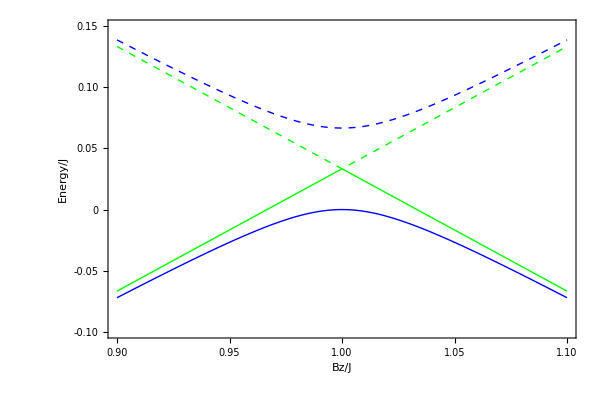

/Users/sina/Google Drive/Research/Singlet Fission Project/21_1n1_Analysis/21_1n1_avoidedCrossing_imagev2.png

```mathematica
export=True;
eigs1=Eigenvalues[LittleH[0.1,0.1/3,β,δ]]/.{ϕ->Pi/2,θ->Pi/2,β->Pi};
eigs2=Eigenvalues[LittleH[0.1,0.1/3,β,δ]]/.{ϕ->Pi/2,θ->Pi/2,β->Pi/2};
Plot[{eigs1[[1]],eigs1[[2]],eigs2[[1]],eigs2[[2]]},{δ,0.9,1.1},PlotLabel->Style["",Black,28],PlotRange->{{0.9,1.1},{-0.10,0.15}}(*,PlotLegends->Placed[plotLegend,{1.1,0.6}]*), Frame->{{True,False},{True,False}},FrameLabel->{{Style["Energy/J",Black,28],None},{Style["Bz/J",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {600,400},AspectRatio->Full,PlotStyle->{{Green,Thick},{Green,Dashed,Thick},{Blue,Thick},{Blue,Thick,Dashed}}(*,Epilog->transitionPoints*)]
If[export,Export["/Users/sina/Google Drive/Research/Singlet Fission Project/21_1n1_Analysis/21_1n1_avoidedCrossing_imagev2.png",%,ImageResolution->500],Print["Image not exported"]]
```

Make a 3D plot

```mathematica
Plot3D[Evaluate[{EpParallel[0.1,-0.1/3,β,δ],EmParallel[0.1,0.1/3,β,δ]}],{δ,0.9,1.1},{β,0,2Pi}]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate[Eigenvalues[LittleH[0.1,-0.1/3,β,δ]/.{ϕ->Pi/2,θ->Pi/2}]],{δ,0.9,1.1},{β,0,2Pi}]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate[Eigenvalues[LittleH[0.1,-0.1/3,Pi,δ]]/.{ϕ->ϕt,θ->Pi/2}],{δ,0.9,1.1},{ϕt,0,Pi}]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate[{Ep[0.1,0.1/3,β,ϵ],Em[0.1,0.1/3,β,ϵ]}/.{θ->0,ϕ->0}],{ϵ,0.9,1.1},{β,0,Pi},BaseStyle->{16,Black,FontFamily->"Avenir"},LabelStyle->Directive[Blend[{Black,White},0.3]],AxesLabel->{Style["B_z/J",20,Black,FontFamily->"Big Caslon"],Style["β",20,Black,FontFamily->"Big Caslon"],Style["E/J",20,Black,FontFamily->"Big Caslon"]},PlotLabel->Style["B || z",26,Black,FontFamily->"Times"],
PlotStyle->{Directive[RGBColor[0.61,0.17,0.58],Specularity[White,50]],Directive[RGBColor[0.,0.62,1.],Specularity[White,50]]},Boxed->False,ImageSize->{800,400},PlotTheme->"ZMesh",Mesh->15,MeshStyle->{Blend[{Black,White},0.9]}(*,BoundaryStyle->None*),PerformanceGoal->"Quality",Ticks->{Automatic,{0,π/4,π/2,3π/4,π}},FaceGrids->{{{-1,0,0},{{0,Pi/4,Pi/2,3Pi/4,Pi},{-0.05,0,0.05,0.1,0.143}}},{{0,-1,0},{{0.9,0.95,1,1.05,1.1},{-0.05,0,0.05,0.1}}},{{0,0,-1},{{0.9,0.95,1,1.05,1.1},{0,Pi/4,Pi/2,3Pi/4,Pi}}}},FaceGridsStyle->Directive[Black],Background->White,Lighting->"Standard",ViewVertical->{0,0,1},ViewPoint->{10,4,2.5},PlotPoints->50]
Export["/Users/sina/Google Drive/Research/Singlet Fission Project/22_10_avoidedCrossing_3Dimage_Bparallely.png",%,ImageResolution->500]
Plot3D[Evaluate[{Ep[0.1,0.0,β,ϵ],Em[0.1,0.0,β,ϵ]}/.{θ->Pi/2,ϕ->Pi/2}],{ϵ,0.9,1.1},{β,0,Pi},BaseStyle->{16,Black,FontFamily->"Avenir"},LabelStyle->Directive[Blend[{Black,White},0.3]],AxesLabel->{Style["B_z/J",20,Black,FontFamily->"Big Caslon"],Style["β",20,Black,FontFamily->"Big Caslon"],Style["E/J",20,Black,FontFamily->"Big Caslon"]},PlotLabel->Style["B || z",26,Black,FontFamily->"Times"],
PlotStyle->{Directive[RGBColor[0.61,0.17,0.58],Specularity[White,50]],Directive[RGBColor[0.,0.62,1.],Specularity[White,50]]},Boxed->False,ImageSize->{800,400},PlotTheme->"ZMesh",Mesh->15,MeshStyle->{Blend[{Black,White},0.9]}(*,BoundaryStyle->None*),PerformanceGoal->"Quality",Ticks->{Automatic,{0,π/4,π/2,3π/4,π}},FaceGrids->{{{-1,0,0},{{0,Pi/4,Pi/2,3Pi/4,Pi},{-0.05,0,0.05,0.1,0.143}}},{{0,-1,0},{{0.9,0.95,1,1.05,1.1},{-0.05,0,0.05,0.1}}},{{0,0,-1},{{0.9,0.95,1,1.05,1.1},{0,Pi/4,Pi/2,3Pi/4,Pi}}}},FaceGridsStyle->Directive[Black],Background->White,Lighting->"Standard",ViewVertical->{0,0,1},ViewPoint->{10,4,2.5},PlotPoints->50]
Export["/Users/sina/Google Drive/Research/Singlet Fission Project/22_10_avoidedCrossing_3Dimage_Bparallely.png",%,ImageResolution->500](*
Export["C:\\Users\\Sina\\Google Drive\\Research\\Singlet Fission Project\\21_1n1_avoidedCrossing_3Dimage.png",%,ImageResolution->500];*)
```

-Graphics3D-

/Users/sina/Google Drive/Research/Singlet Fission Project/22_10_avoidedCrossing_3Dimage_Bparallely.png

-Graphics3D-

/Users/sina/Google Drive/Research/Singlet Fission Project/22_10_avoidedCrossing_3Dimage_Bparallely.png

```mathematica
Plot3D[Evaluate[{Ep[0.1,0.1/3,β,δ],Em[0.1,0.1/3,β,δ]}/.{δ->1,ϕ->0}],{θ,0,Pi/2},{β,0,θ},BaseStyle->{16,Black,FontFamily->"Avenir"},LabelStyle->Directive[Blend[{Black,White},0.3]],AxesLabel->{Style["θ",20,Black,FontFamily->"Big Caslon"],Style["β",20,Black,FontFamily->"Big Caslon"],Style["E/J",20,Black,FontFamily->"Big Caslon"]},PlotLabel->Style["Energy Eigenvalues \n B_z/J = 1, ϕ = 0",26,Black,FontFamily->"Times"],PlotStyle->{Directive[RGBColor[0.61,0.17,0.58],Specularity[White,50]],Directive[RGBColor[0.,0.62,1.],Specularity[White,50]]},Boxed->False,ImageSize->{800,400},PlotTheme->"ZMesh",Mesh->15,MeshStyle->{Blend[{Black,White},0.9]}(*,BoundaryStyle->None*),PerformanceGoal->"Quality",Ticks->{Automatic,{0,π/4,π/2,3π/4,π}},FaceGrids->{{-1,0,0},{0,-1,0},{0,0,-1}},FaceGridsStyle->Directive[Black],Background->White,Lighting->"Standard",ViewVertical->{0,0,1},ViewPoint->{4,10,2.5},PlotPoints->50]
```

-Graphics3D-

```mathematica
(* Plot the difference of the energy eigenvalues wrt θ,β at δ=1, ϕ=0*)
Plot3D[Evaluate[(Ep[0.1,0.1/3,β,δ]-Em[0.1,0.1/3,β,δ])/.{δ->1,ϕ->0}],{θ,0,Pi/2},{β,0,Pi},BaseStyle->{16,Black,FontFamily->"Avenir"},LabelStyle->Directive[Blend[{Black,White},0.3]],AxesLabel->{Style["θ",20,Black,FontFamily->"Big Caslon"],Style["β",20,Black,FontFamily->"Big Caslon"],Style["E/J",20,Black,FontFamily->"Big Caslon"]},PlotLabel->Style["Difference of Energy Eigenvalues \n B_z/J = 1, ϕ = 0",26,Black,FontFamily->"Times"],PlotStyle->{Directive[RGBColor[0.61,0.17,0.58]],Directive[RGBColor[0.,0.62,1.]]},Boxed->False,ImageSize->{800,400},PlotTheme->"ZMesh",Mesh->15,MeshStyle->{Blend[{Black,White},0.9]}(*,BoundaryStyle->None*),PerformanceGoal->"Quality",Ticks->{Automatic,{0,π/4,π/2,3π/4,π}},FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}},FaceGridsStyle->Directive[Black],Background->White,Lighting->"Standard",ViewVertical->{0,0,1},PlotPoints->50]
```

-Graphics3D-

```mathematica
(* Plot the difference of the energy eigenvalues wrt θ,β at δ=1, ϕ=π/2*)Plot3D[Evaluate[(Ep[0.1,0.1/3,β,δ]-Em[0.1,0.1/3,β,δ])/.{δ->1,ϕ->Pi/2}],{θ,0,Pi/2},{β,0,Pi},BaseStyle->{16,Black,FontFamily->"Avenir"},LabelStyle->Directive[Blend[{Black,White},0.3]],AxesLabel->{Style["θ",20,Black,FontFamily->"Big Caslon"],Style["β",20,Black,FontFamily->"Big Caslon"],Style["E/J",20,Black,FontFamily->"Big Caslon"]},PlotLabel->Style["Difference of Energy Eigenvalues \n B_z/J = 1, ϕ = π/2",26,Black,FontFamily->"Times"],PlotStyle->{Directive[RGBColor[0.61,0.17,0.58]],Directive[RGBColor[0.,0.62,1.]]},Boxed->False,ImageSize->{800,400},PlotTheme->"ZMesh",Mesh->15,MeshStyle->{Blend[{Black,White},0.9]}(*,BoundaryStyle->None*),PerformanceGoal->"Quality",Ticks->{Automatic,{0,π/4,π/2,3π/4,π}},FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}},FaceGridsStyle->Directive[Black],Background->White,Lighting->"Standard",ViewVertical->{0,0,1},PlotPoints->50]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[Evaluate[(Ep[0.1,0.1/3,β,δ]-Em[0.1,0.1/3,β,δ])/.{δ->1,ϕ->ϕtrue}],{θ,0,Pi/2},{β,0,Pi},BaseStyle->{16,Black,FontFamily->"Avenir"},LabelStyle->Directive[Blend[{Black,White},0.3]],AxesLabel->{Style["θ",20,Black,FontFamily->"Big Caslon"],Style["β",20,Black,FontFamily->"Big Caslon"],Style["E/J",20,Black,FontFamily->"Big Caslon"]},PlotLabel->Style["Difference of Energy Eigenvalues \n B_z/J = 1, ϕ = π/2",26,Black,FontFamily->"Times"],PlotStyle->{Directive[RGBColor[0.61,0.17,0.58]],Directive[RGBColor[0.,0.62,1.]]},Boxed->False,ImageSize->{800,400},PlotTheme->"ZMesh",Mesh->15,MeshStyle->{Blend[{Black,White},0.9]}(*,BoundaryStyle->None*),PerformanceGoal->"Quality",Ticks->{Automatic,{0,π/4,π/2,3π/4,π}},FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}},FaceGridsStyle->Directive[Black],Background->White,Lighting->"Standard",ViewVertical->{0,0,1},PlotPoints->50],{{ϕtrue,0,"ϕ"},0,Pi}]
```

```mathematica
(* Plot the difference of the energy eigenvalues wrt θ,ϕ at δ=1, β=π/2*)Plot3D[Evaluate[(Ep[0.1,0.1/3,β,δ]-Em[0.1,0.1/3,β,δ])/.{δ->1,β->Pi/2}],{θ,0,Pi},{ϕ,0,Pi},BaseStyle->{16,Black,FontFamily->"Avenir"},LabelStyle->Directive[Blend[{Black,White},0.3]],AxesLabel->{Style["θ",20,Black,FontFamily->"Big Caslon"],Style["ϕ",20,Black,FontFamily->"Big Caslon"],Style["E/J",20,Black,FontFamily->"Big Caslon"]},PlotLabel->Style["Difference of Energy Eigenvalues \n B_z/J = 1, β = π/2",26,Black,FontFamily->"Times"],PlotStyle->{Directive[RGBColor[0.61,0.17,0.58]],Directive[RGBColor[0.,0.62,1.]]},Boxed->False,ImageSize->{800,400},PlotTheme->"ZMesh",Mesh->15,MeshStyle->{Blend[{Black,White},0.9]}(*,BoundaryStyle->None*),PerformanceGoal->"Quality",Ticks->{Automatic,{0,π/4,π/2,3π/4,π}},FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}},FaceGridsStyle->Directive[Black],Background->White,Lighting->"Standard",ViewVertical->{0,0,1},PlotPoints->50]
```

-Graphics3D-

```mathematica
derivative=FullSimplify[D[(Ep[0.1,0.1/3,β,δ]-Em[0.1,0.1/3,β,δ]),β]/.δ->1]
```

(Sin[2 β] Sin[θ]^2 (0.0133333+0.00444444 Cos[2 θ]-0.00888889 Cos[2 ϕ] Sin[θ]^2))/(√(0.0444444-0.00888889 (2 Cos[4 θ] Cos[ϕ]^2+4 Cos[2 β] (3+Cos[2 θ]) Sin[θ]^2+Cos[2 ϕ] (3-8 Cos[2 β] Sin[θ]^4)+8 Cos[2 θ] Sin[ϕ]^2)))

```mathematica
list=NumeratorDenominator[derivative]
```

{Sin[2 β] Sin[θ]^2 (0.0133333+0.00444444 Cos[2 θ]-0.00888889 Cos[2 ϕ] Sin[θ]^2),√(0.0444444-0.00888889 (2 Cos[4 θ] Cos[ϕ]^2+4 Cos[2 β] (3+Cos[2 θ]) Sin[θ]^2+Cos[2 ϕ] (3-8 Cos[2 β] Sin[θ]^4)+8 Cos[2 θ] Sin[ϕ]^2))}

```mathematica
ContourPlot3D[list[[1]]==0,{ϕ,0,Pi/2},{θ,0,Pi/2},{β,0,Pi},BaseStyle->{18,Black,FontFamily->"Avenir"},LabelStyle->Directive[Blend[{Black,White},0.3]],AxesLabel->{Style["θ",24,Black,FontFamily->"Avenir"],Style["β",24,Black,FontFamily->"Avenir"],Style["ϕ",24,Black,FontFamily->"Avenir"]},Boxed->False,ImageSize->{800,400},PlotTheme->"ZMesh",Mesh->15,MeshStyle->{Blend[{Black,White},0.9]}(*,BoundaryStyle->None*),PerformanceGoal->"Quality",Ticks->{Automatic,{0,π/4,π/2,3π/4,π}},FaceGrids->{{-1,0,0},{0,-1,0},{0,0,-1}},FaceGridsStyle->Directive[Black],Background->White,Lighting->"Standard",ViewVertical->{0,0,1},ViewPoint->{10,4,2.5},PlotPoints->50]
```

-Graphics3D-

```mathematica
ContourPlot3D[list[[2]]==0,{ϕ,0,Pi/2},{θ,0,Pi/2},{β,0,Pi},BaseStyle->{18,Black,FontFamily->"Avenir"},LabelStyle->Directive[Blend[{Black,White},0.3]],AxesLabel->{Style["θ",24,Black,FontFamily->"Avenir"],Style["β",24,Black,FontFamily->"Avenir"],Style["ϕ",24,Black,FontFamily->"Avenir"]},Boxed->False,ImageSize->{800,400},PlotTheme->"ZMesh",Mesh->15,MeshStyle->{Blend[{Black,White},0.9]}(*,BoundaryStyle->None*),PerformanceGoal->"Quality",Ticks->{Automatic,{0,π/4,π/2,3π/4,π}},FaceGrids->{{-1,0,0},{0,-1,0},{0,0,-1}},FaceGridsStyle->Directive[Black],Background->White,Lighting->"Standard",ViewVertical->{0,0,1},ViewPoint->{10,4,2.5},PlotPoints->50]
```

-Graphics3D-

```mathematica
list[[2]]
```

√(0.0444444-0.00888889 (2 Cos[4 θ] Cos[ϕ]^2+4 Cos[2 β] (3+Cos[2 θ]) Sin[θ]^2+Cos[2 ϕ] (3-8 Cos[2 β] Sin[θ]^4)+8 Cos[2 θ] Sin[ϕ]^2))

```mathematica
stepSize=0.01;
dataEm[ϕvar_,θvar_]:=Table[Table[EmParallel[0.1,0.1/3,β,δ]/.{ϕ->ϕvar,θ->θvar},{δ,0.9,1.1,stepSize}],{β,0,Pi,stepSize}];
dataEp[ϕvar_,θvar_]:=Table[Table[EpParallel[0.1,0.1/3,β,δ]/.{ϕ->ϕvar,θ->θvar},{δ,0.9,1.1,stepSize}],{β,0,Pi,stepSize}];
Export["/Users/sina/Google Drive/Research/Singlet Fission Project/21_1n1_Analysis/Data Files/21_1n1_avoidedCrossing_3Ddata_Bparallely_Em.txt",dataEm[Pi/2,Pi/2],"Table"];
Export["/Users/sina/Google Drive/Research/Singlet Fission Project/21_1n1_Analysis/Data Files/21_1n1_avoidedCrossing_3Ddata_Bparallely_Ep.txt",dataEp[Pi/2,Pi/2],"Table"];
(*Export["/Users/sina/Google Drive/Research/Singlet Fission Project/21_1n1_Analysis/Data Files/21_1n1_avoidedCrossing_3Ddata_Bparallelz_Em.txt",dataEm[0,0],"Table"];
Export["/Users/sina/Google Drive/Research/Singlet Fission Project/21_1n1_Analysis/Data Files/21_1n1_avoidedCrossing_3Ddata_Bparallelz_Ep.txt",dataEp[0,0],"Table"];*)
```

```mathematica
dataEm[ϕ,θ]
```

{{1/48 (0.2 (1+3 Cos[2 θ])-0.4 Cos[2 ϕ] Sin[θ]^2-6. (0.0333333+0.1 Cos[2 θ]+0.2 Cos[2 ϕ] Sin[θ]^2)-3 √(10.2844-0.00888889 (2 Cos[4 θ] Cos[ϕ]^2+4. (3+Cos[2 θ]) Sin[θ]^2+Cos[2 ϕ] (3-8. Sin[θ]^4)+8 Cos[2 θ] Sin[ϕ]^2))),79,1/48 (0.2 (1+3 Cos[2 θ])-0.4 Cos[2 ϕ] Sin[θ]^2-6. (0.0333333+0.1 Cos[2 θ]+0.2 Cos[2 ϕ] Sin[θ]^2)-3 √(10.2844-0.00888889 (2 Cos[4 θ] Cos[ϕ]^2+4. (3+Cos[2 θ]) Sin[θ]^2+Cos[2 ϕ] (3-8. Sin[θ]^4)+8 Cos[2 θ] Sin[ϕ]^2)))},627,{1/48 (1),79,1/48 (-0.4 (1+3 Cos[2 θ])-1-23 1-3 √(10.2844-0.00888889 (2 Cos[4 θ] Cos[ϕ]^2+1+1 1+8 Cos[2 θ] Sin[ϕ]^2)))}}
 |  |  |  |

```mathematica
export=False;
Plot3D[Evaluate[Ep[0.1,0.1/3,β,ϵ]-Em[0.1,0.1/3,β,ϵ]/.{θ->Pi/2,ϕ->Pi/2}],{ϵ,0.9,1.1},{β,0,Pi},AxesLabel->{Style["B/J",20,Black],Style["β",20,Black],Style["E/J",20,Black]},Boxed->False,ImageSize->{800,400}]
If[export,Export["C:\\Users\\Sina\\Google Drive\\Research\\Singlet Fission Project\\21_1n1_avoidedCrossing_energyDiff_3Dimage.png",%,ImageResolution->500];,Print["Image not saved"]]
```

-Graphics3D-

Image not saved

Analyze the allowed transitions

```mathematica
(* DIAGONALIZATION OF HAMILTONIAN *)
(* Re-arrange Hamiltonian so |1,-1⟩ and |2,1⟩ are next to each other *)
Uswap = IdentityMatrix[9];
Uswap[[5;;6]]={Uswap[[6]],Uswap[[5]]}
Uswap//MatrixForm
Hswapped=Uswap.H[ϕ,θ,β,δ].Transpose[Uswap];
%//MatrixForm
```

{{0,0,0,0,0,1,0,0,0},{0,0,0,0,1,0,0,0,0}}

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(2 | 0 | 0 | 0 | -((d-e) ⅇ^(ⅈ ϕ) Cos[β] Sin[β+2 θ])/(√3) | (ⅇ^(2 ⅈ ϕ) (d+3 e+(-d+e) Cos[β] Cos[β+2 θ]))/(2 √3) | (d+3 e+3 (d-e) Cos[β] Cos[β+2 θ])/(3 √2) | ((d-e) ⅇ^(-ⅈ ϕ) Cos[β] Sin[β+2 θ])/(√3) | (ⅇ^(-2 ⅈ ϕ) (d+3 e+(-d+e) Cos[β] Cos[β+2 θ]))/(2 √3)
0 | 1-d/12-e/4+δ+1/4 (-d+e) Cos[β] Cos[β+2 θ] | ((-d+e) ⅇ^(-ⅈ ϕ) Cos[β] Sin[β+2 θ])/(2 √2) | 1/4 ⅇ^(-2 ⅈ ϕ) (d+3 e+(-d+e) Cos[β] Cos[β+2 θ]) | 3/4 (d-e) Sin[β] Sin[β+2 θ] | 1/2 (d-e) ⅇ^(ⅈ ϕ) Cos[β+2 θ] Sin[β] | 1/2 √(3/2) (-d+e) ⅇ^(-ⅈ ϕ) Cos[β+2 θ] Sin[β] | 1/4 (-d+e) ⅇ^(-2 ⅈ ϕ) Sin[β] Sin[β+2 θ] | 0
0 | -((d-e) ⅇ^(ⅈ ϕ) Cos[β] Sin[β+2 θ])/(2 √2) | 1/6 (6+d+3 e+3 (d-e) Cos[β] Cos[β+2 θ]) | ((-d+e) ⅇ^(-ⅈ ϕ) Cos[β] Sin[β+2 θ])/(2 √2) | -((d-e) ⅇ^(ⅈ ϕ) Cos[β+2 θ] Sin[β])/(2 √2) | ((d-e) ⅇ^(2 ⅈ ϕ) Sin[β] Sin[β+2 θ])/(2 √2) | 0 | ((-d+e) ⅇ^(-ⅈ ϕ) Cos[β+2 θ] Sin[β])/(2 √2) | ((-d+e) ⅇ^(-2 ⅈ ϕ) Sin[β] Sin[β+2 θ])/(2 √2)
0 | 1/4 ⅇ^(2 ⅈ ϕ) (d+3 e+(-d+e) Cos[β] Cos[β+2 θ]) | -((d-e) ⅇ^(ⅈ ϕ) Cos[β] Sin[β+2 θ])/(2 √2) | 1/24 (-2 (d+3 (-4+e+4 δ))+6 (-d+e) Cos[β] Cos[β+2 θ]) | -1/4 (d-e) ⅇ^(2 ⅈ ϕ) Sin[β] Sin[β+2 θ] | 0 | 1/2 √(3/2) (d-e) ⅇ^(ⅈ ϕ) Cos[β+2 θ] Sin[β] | 3/4 (d-e) Sin[β] Sin[β+2 θ] | 1/2 (-d+e) ⅇ^(-ⅈ ϕ) Cos[β+2 θ] Sin[β]
((-d+e) ⅇ^(-ⅈ ϕ) Cos[β] Sin[β+2 θ])/(√3) | 3/4 (d-e) Sin[β] Sin[β+2 θ] | ((-d+e) ⅇ^(-ⅈ ϕ) Cos[β+2 θ] Sin[β])/(2 √2) | 1/4 (-d+e) ⅇ^(-2 ⅈ ϕ) Sin[β] Sin[β+2 θ] | 1/24 (-2 (d+3 (4+e-4 δ))+6 (-d+e) Cos[β] Cos[β+2 θ]) | 1/2 (d-e) ⅇ^(ⅈ ϕ) Cos[β] Sin[β+2 θ] | ((d-e) ⅇ^(-ⅈ ϕ) Cos[β] Sin[β+2 θ])/(2 √6) | 1/4 ⅇ^(-2 ⅈ ϕ) (d+3 e+(-d+e) Cos[β] Cos[β+2 θ]) | 0
(ⅇ^(-2 ⅈ ϕ) (d+3 e+(-d+e) Cos[β] Cos[β+2 θ]))/(2 √3) | 1/2 (d-e) ⅇ^(-ⅈ ϕ) Cos[β+2 θ] Sin[β] | ((d-e) ⅇ^(-2 ⅈ ϕ) Sin[β] Sin[β+2 θ])/(2 √2) | 0 | 1/2 (d-e) ⅇ^(-ⅈ ϕ) Cos[β] Sin[β+2 θ] | -1+2 δ+1/6 (d+3 e+3 (d-e) Cos[β] Cos[β+2 θ]) | (ⅇ^(-2 ⅈ ϕ) (d+3 e+(-d+e) Cos[β] Cos[β+2 θ]))/(2 √6) | 0 | 0
(d+3 e+3 (d-e) Cos[β] Cos[β+2 θ])/(3 √2) | -1/2 √(3/2) (d-e) ⅇ^(ⅈ ϕ) Cos[β+2 θ] Sin[β] | 0 | 1/2 √(3/2) (d-e) ⅇ^(-ⅈ ϕ) Cos[β+2 θ] Sin[β] | ((d-e) ⅇ^(ⅈ ϕ) Cos[β] Sin[β+2 θ])/(2 √6) | (ⅇ^(2 ⅈ ϕ) (d+3 e+(-d+e) Cos[β] Cos[β+2 θ]))/(2 √6) | 1/12 (-2 (6+d+3 e)+6 (-d+e) Cos[β] Cos[β+2 θ]) | ((-d+e) ⅇ^(-ⅈ ϕ) Cos[β] Sin[β+2 θ])/(2 √6) | (ⅇ^(-2 ⅈ ϕ) (d+3 e+(-d+e) Cos[β] Cos[β+2 θ]))/(2 √6)
((d-e) ⅇ^(ⅈ ϕ) Cos[β] Sin[β+2 θ])/(√3) | -1/4 (d-e) ⅇ^(2 ⅈ ϕ) Sin[β] Sin[β+2 θ] | -((d-e) ⅇ^(ⅈ ϕ) Cos[β+2 θ] Sin[β])/(2 √2) | 3/4 (d-e) Sin[β] Sin[β+2 θ] | 1/4 ⅇ^(2 ⅈ ϕ) (d+3 e+(-d+e) Cos[β] Cos[β+2 θ]) | 0 | -((d-e) ⅇ^(ⅈ ϕ) Cos[β] Sin[β+2 θ])/(2 √6) | 1/24 (-2 (d+3 (4+e+4 δ))+6 (-d+e) Cos[β] Cos[β+2 θ]) | 1/2 (-d+e) ⅇ^(-ⅈ ϕ) Cos[β] Sin[β+2 θ]
(ⅇ^(2 ⅈ ϕ) (d+3 e+(-d+e) Cos[β] Cos[β+2 θ]))/(2 √3) | 0 | -((d-e) ⅇ^(2 ⅈ ϕ) Sin[β] Sin[β+2 θ])/(2 √2) | -1/2 (d-e) ⅇ^(ⅈ ϕ) Cos[β+2 θ] Sin[β] | 0 | 0 | (ⅇ^(2 ⅈ ϕ) (d+3 e+(-d+e) Cos[β] Cos[β+2 θ]))/(2 √6) | -1/2 (d-e) ⅇ^(ⅈ ϕ) Cos[β] Sin[β+2 θ] | -1-2 δ+1/6 (d+3 e+3 (d-e) Cos[β] Cos[β+2 θ]))

```mathematica
eigs=Eigenvectors[LittleH[d,e,β,δ]];
soln={FullSimplify[Normalize[eigs[[1]]],Assumptions->{δ∈ Reals,e ∈ Reals,d ∈ Reals,β ∈ Reals,δ>0,β>0,β≤Pi,d>e}],FullSimplify[Normalize[eigs[[2]]],Assumptions->{δ∈ Reals,e ∈ Reals,d ∈ Reals,β ∈ Reals,δ>0,β>0,β≤Pi,d>e}]}
```

{{(Csc[β] Csc[β+2 θ] (8 ⅇ^(2 ⅈ ϕ) (-1+δ)+√(ⅇ^(4 ⅈ ϕ) ((d-e)^2+64 (-1+δ)^2-(d-e)^2 (Cos[2 β]+2 Cos[2 β+4 θ] Sin[β]^2)))))/(√(4 (d-e)^2+Abs[Csc[β]^2 Csc[β+2 θ]^2 (8 ⅇ^(2 ⅈ ϕ) (-1+δ)+√(ⅇ^(4 ⅈ ϕ) ((d-e)^2+64 (-1+δ)^2-(d-e)^2 (Cos[2 β]+2 Cos[2 β+4 θ] Sin[β]^2))))^2])),2/(√(4+Abs[(Csc[β] Csc[β+2 θ] (8 ⅇ^(2 ⅈ ϕ) (-1+δ)+√(ⅇ^(4 ⅈ ϕ) ((d-e)^2+64 (-1+δ)^2-(d-e)^2 (Cos[2 β]+2 Cos[2 β+4 θ] Sin[β]^2)))))/(d-e)]^2))},{(Csc[β] Csc[β+2 θ] (16 ⅇ^(2 ⅈ ϕ) (-1+δ)-2 √(ⅇ^(4 ⅈ ϕ) ((d-e)^2+64 (-1+δ)^2-(d-e)^2 (Cos[2 β]+2 Cos[2 β+4 θ] Sin[β]^2)))))/(2 √(4 (d-e)^2+Abs[Csc[β]^2 Csc[β+2 θ]^2 (-8 ⅇ^(2 ⅈ ϕ) (-1+δ)+√(ⅇ^(4 ⅈ ϕ) ((d-e)^2+64 (-1+δ)^2-(d-e)^2 (Cos[2 β]+2 Cos[2 β+4 θ] Sin[β]^2))))^2])),2/(√(4+Abs[(Csc[β] Csc[β+2 θ] (-8 ⅇ^(2 ⅈ ϕ) (-1+δ)+√(ⅇ^(4 ⅈ ϕ) ((d-e)^2+64 (-1+δ)^2-(d-e)^2 (Cos[2 β]+2 Cos[2 β+4 θ] Sin[β]^2)))))/(d-e)]^2))}}

```mathematica
soln/.δ->1
```

{{(Csc[β] Csc[β+2 θ] √(ⅇ^(4 ⅈ ϕ) ((d-e)^2-(d-e)^2 (Cos[2 β]+2 Cos[2 β+4 θ] Sin[β]^2))))/(√(4 (d-e)^2+ⅇ^(-4 Im[ϕ]) Abs[Csc[β]^2 Csc[β+2 θ]^2 ((d-e)^2-(d-e)^2 (Cos[2 β]+2 Cos[2 β+4 θ] Sin[β]^2))])),2/(√(4+ⅇ^(-4 Im[ϕ]) Abs[(Csc[β] Csc[β+2 θ])/(d-e)]^2 Abs[(d-e)^2-(d-e)^2 (Cos[2 β]+2 Cos[2 β+4 θ] Sin[β]^2)]))},{-((Csc[β] Csc[β+2 θ] √(ⅇ^(4 ⅈ ϕ) ((d-e)^2-(d-e)^2 (Cos[2 β]+2 Cos[2 β+4 θ] Sin[β]^2))))/(√(4 (d-e)^2+ⅇ^(-4 Im[ϕ]) Abs[Csc[β]^2 Csc[β+2 θ]^2 ((d-e)^2-(d-e)^2 (Cos[2 β]+2 Cos[2 β+4 θ] Sin[β]^2))]))),2/(√(4+ⅇ^(-4 Im[ϕ]) Abs[(Csc[β] Csc[β+2 θ])/(d-e)]^2 Abs[(d-e)^2-(d-e)^2 (Cos[2 β]+2 Cos[2 β+4 θ] Sin[β]^2)]))}}

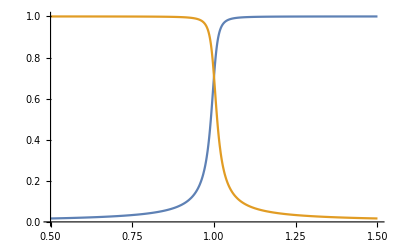

```mathematica
Plot[Evaluate[{soln[[1]][[1]],-soln[[2]][[1]]}/.{d->0.1,e->0.1/3,β->Pi/2,θ->0,ϕ->0}],{δ,0.5,1.5}]
```

```mathematica
(*Define matrix to take |1,-1⟩ and |2,1⟩ to linear combinations of each other *)
Udiag=IdentityMatrix[9];
Udiag[[4;;5]]={{0,0,0,soln[[1]][[1]],soln[[2]][[1]],0,0,0,0},{0,0,0,soln[[1]][[2]],soln[[2]][[2]],0,0,0,0}}/.{β->Pi/2};
(*Udiag[[4;;5]]=1/Sqrt[2]{{0,0,0,1,-1,0,0,0,0},{0,0,0,1,1,0,0,0,0}};*)
Udiag//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ((8 ⅇ^(2 ⅈ ϕ) (-1+δ)+√(ⅇ^(4 ⅈ ϕ) ((d-e)^2+64 (-1+δ)^2-(d-e)^2 (-1-2 Cos[4 θ])))) Sec[2 θ])/(√(4 (d-e)^2+Abs[(8 ⅇ^(2 ⅈ ϕ) (-1+δ)+√(ⅇ^(4 ⅈ ϕ) ((d-e)^2+64 (-1+δ)^2-(d-e)^2 (-1-2 Cos[4 θ]))))^2 Sec[2 θ]^2])) | ((16 ⅇ^(2 ⅈ ϕ) (-1+δ)-2 √(ⅇ^(4 ⅈ ϕ) ((d-e)^2+64 (-1+δ)^2-(d-e)^2 (-1-2 Cos[4 θ])))) Sec[2 θ])/(2 √(4 (d-e)^2+Abs[(-8 ⅇ^(2 ⅈ ϕ) (-1+δ)+√(ⅇ^(4 ⅈ ϕ) ((d-e)^2+64 (-1+δ)^2-(d-e)^2 (-1-2 Cos[4 θ]))))^2 Sec[2 θ]^2])) | 0 | 0 | 0 | 0
0 | 0 | 0 | 2/(√(4+Abs[((8 ⅇ^(2 ⅈ ϕ) (-1+δ)+√(ⅇ^(4 ⅈ ϕ) ((d-e)^2+64 (-1+δ)^2-(d-e)^2 (-1-2 Cos[4 θ])))) Sec[2 θ])/(d-e)]^2)) | 2/(√(4+Abs[((-8 ⅇ^(2 ⅈ ϕ) (-1+δ)+√(ⅇ^(4 ⅈ ϕ) ((d-e)^2+64 (-1+δ)^2-(d-e)^2 (-1-2 Cos[4 θ])))) Sec[2 θ])/(d-e)]^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
transitionZFS=FullSimplify[Udiag.Hswapped.Transpose[Udiag]/.{δ->1,β->Pi/2}];
%//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | ((d+3 e) ⅇ^(2 ⅈ ϕ))/(2 √3) | (d+3 e)/(3 √2) | 0 | ((d+3 e) ⅇ^(-2 ⅈ ϕ))/(2 √3)
0 | 2-d/12-e/4 | 0 | (ⅇ^(-2 ⅈ ϕ) √((d-e)^2 ⅇ^(4 ⅈ ϕ) (1+Cos[4 θ])) (-3 (d-e) ⅇ^(2 ⅈ ϕ)+(d+3 e) Sec[2 θ]))/(8 √((d-e) Re[d-e])) | (ⅇ^(-2 ⅈ ϕ) (d+3 e+3 (d-e) ⅇ^(2 ⅈ ϕ) Cos[2 θ]))/(4 √2) | -(d-e) ⅇ^(ⅈ ϕ) Cos[θ] Sin[θ] | √(3/2) (d-e) ⅇ^(-ⅈ ϕ) Cos[θ] Sin[θ] | 1/4 (-d+e) ⅇ^(-2 ⅈ ϕ) Cos[2 θ] | 0
0 | 0 | 1/6 (6+d+3 e) | -((d-e) ⅇ^(ⅈ ϕ) √((d-e)^2 ⅇ^(4 ⅈ ϕ) (1+Cos[4 θ])) Tan[2 θ])/(4 √((d-e) (d+Conjugate[d]-2 Re[e]))) | 1/4 (d-e) ⅇ^(ⅈ ϕ) Sin[2 θ] | ((d-e) ⅇ^(2 ⅈ ϕ) Cos[2 θ])/(2 √2) | 0 | ((d-e) ⅇ^(-ⅈ ϕ) Cos[θ] Sin[θ])/(√2) | ((-d+e) ⅇ^(-2 ⅈ ϕ) Cos[2 θ])/(2 √2)
0 | (√((d-e)^2 ⅇ^(4 ⅈ ϕ) (1+Cos[4 θ])) (-3 d+3 e+(d+3 e) ⅇ^(2 ⅈ ϕ) Sec[2 θ]))/(8 √((d-e) Re[d-e])) | ((-d+e) ⅇ^(-ⅈ ϕ) √((d-e)^2 ⅇ^(4 ⅈ ϕ) (1+Cos[4 θ])) Tan[2 θ])/(4 √((d-e) (d+Conjugate[d]-2 Re[e]))) | ((d-e) ⅇ^(2 ⅈ ϕ) (-2 (d+3 e) ⅇ^(2 ⅈ ϕ)+3 (d-e) (1+ⅇ^(4 ⅈ ϕ)) Cos[2 θ]))/(24 Re[d-e]) | -(ⅈ (d-e) √((d-e)^2 ⅇ^(4 ⅈ ϕ) (1+Cos[4 θ])) Sin[2 ϕ])/(4 √((d-e) (d+Conjugate[d]-2 Re[e]))) | 0 | -(√(3/2) (d-e) ⅇ^(ⅈ ϕ) √((d-e)^2 ⅇ^(4 ⅈ ϕ) Cos[2 θ]^2) Tan[2 θ])/(2 √((d-e) (d+Conjugate[d]-2 Re[e]))) | (ⅇ^(-2 ⅈ ϕ) √((d-e)^2 ⅇ^(4 ⅈ ϕ) (1+Cos[4 θ])) (3 (d-e) ⅇ^(2 ⅈ ϕ)-(d+3 e) Sec[2 θ]))/(8 √((d-e) Re[d-e])) | ((d-e) ⅇ^(-ⅈ ϕ) √((d-e)^2 ⅇ^(4 ⅈ ϕ) (1+Cos[4 θ])) Tan[2 θ])/(4 √((d-e) Re[d-e]))
0 | ((d+3 e) ⅇ^(2 ⅈ ϕ)+3 (d-e) Cos[2 θ])/(4 √2) | 1/4 (d-e) ⅇ^(-ⅈ ϕ) Sin[2 θ] | (ⅈ (d-e) √((d-e)^2 ⅇ^(4 ⅈ ϕ) (1+Cos[4 θ])) Sin[2 ϕ])/(4 √((d-e) (d+Conjugate[d]-2 Re[e]))) | 1/12 (-d-3 e+3 (-d+e) Cos[2 θ] Cos[2 ϕ]) | 0 | -1/4 √3 (d-e) ⅇ^(ⅈ ϕ) Sin[2 θ] | (ⅇ^(-2 ⅈ ϕ) (d+3 e+3 (d-e) ⅇ^(2 ⅈ ϕ) Cos[2 θ]))/(4 √2) | ((d-e) ⅇ^(-ⅈ ϕ) Cos[θ] Sin[θ])/(√2)
((d+3 e) ⅇ^(-2 ⅈ ϕ))/(2 √3) | (-d+e) ⅇ^(-ⅈ ϕ) Cos[θ] Sin[θ] | ((d-e) ⅇ^(-2 ⅈ ϕ) Cos[2 θ])/(2 √2) | 0 | 0 | 1/6 (6+d+3 e) | ((d+3 e) ⅇ^(-2 ⅈ ϕ))/(2 √6) | 0 | 0
(d+3 e)/(3 √2) | √(3/2) (d-e) ⅇ^(ⅈ ϕ) Cos[θ] Sin[θ] | 0 | (√(3/2) (-d+e) ⅇ^(-ⅈ ϕ) √((d-e)^2 ⅇ^(4 ⅈ ϕ) Cos[2 θ]^2) Tan[2 θ])/(2 √((d-e) (d+Conjugate[d]-2 Re[e]))) | 1/2 √3 (-d+e) ⅇ^(-ⅈ ϕ) Cos[θ] Sin[θ] | ((d+3 e) ⅇ^(2 ⅈ ϕ))/(2 √6) | 1/6 (-d-3 (2+e)) | 0 | ((d+3 e) ⅇ^(-2 ⅈ ϕ))/(2 √6)
0 | -1/4 (d-e) ⅇ^(2 ⅈ ϕ) Cos[2 θ] | ((d-e) ⅇ^(ⅈ ϕ) Cos[θ] Sin[θ])/(√2) | -(√((d-e)^2 ⅇ^(4 ⅈ ϕ) (1+Cos[4 θ])) (-3 d+3 e+(d+3 e) ⅇ^(2 ⅈ ϕ) Sec[2 θ]))/(8 √((d-e) Re[d-e])) | ((d+3 e) ⅇ^(2 ⅈ ϕ)+3 (d-e) Cos[2 θ])/(4 √2) | 0 | 0 | 1/12 (-d-3 (8+e)) | 0
((d+3 e) ⅇ^(2 ⅈ ϕ))/(2 √3) | 0 | -((d-e) ⅇ^(2 ⅈ ϕ) Cos[2 θ])/(2 √2) | ((d-e) ⅇ^(ⅈ ϕ) √((d-e)^2 ⅇ^(4 ⅈ ϕ) (1+Cos[4 θ])) Tan[2 θ])/(4 √((d-e) Re[d-e])) | ((d-e) ⅇ^(ⅈ ϕ) Cos[θ] Sin[θ])/(√2) | 0 | ((d+3 e) ⅇ^(2 ⅈ ϕ))/(2 √6) | 0 | 1/6 (d+3 (-6+e)))

A transition due to an externally applied perpendicular magnetic field will be proportional to  |⟨α|S_x|β⟩|^2 a la Fermi’s golden rule.

```mathematica
vecList
```

{|0,0⟩,|1,1⟩,|1,0⟩,|1,-1⟩,|2,2⟩,|2,1⟩,|2,0⟩,|2,-1⟩,|2,-2⟩}

```mathematica
vecs={{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1},{0,0,0,1/Sqrt[2],0,1/Sqrt[2],0,0,0}}
Table[Abs[vecs[[i]].(UtotSpin.(sAx+sBx).Transpose[UtotSpin]).{0,0,0,1/Sqrt[2],0,1/Sqrt[2],0,0,0}]^2,{i,1,8}]
```

{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1},{0,0,0,1/(√2),0,1/(√2),0,0,0}}

{0,0,1/4,1/2,3/4,0,0,0}

```mathematica
(UtotSpin.(sAx+sBx).Transpose[UtotSpin])//MatrixForm
(UtotSpin.(sAx+sBx).Transpose[UtotSpin])*(UtotSpin.(sAx+sBx).Transpose[UtotSpin])//MatrixForm
FullSimplify[MatrixPower[(UtotSpin.(sAx+sBx).Transpose[UtotSpin]),2]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | √(2/3)+1/(√6) | 0 | 0
0 | 0 | 0 | 0 | 0 | √(3/2) | 0 | √(3/2) | 0
0 | 0 | 0 | 0 | 0 | 0 | √(2/3)+1/(√6) | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | (√(2/3)+1/(√6))^2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/2 | 0 | 3/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | (√(2/3)+1/(√6))^2 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | √(3/2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 5/2 | 0 | 3/2 | 0
0 | 0 | 0 | 0 | √(3/2) | 0 | 3 | 0 | √(3/2)
0 | 0 | 0 | 0 | 0 | 3/2 | 0 | 5/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | √(3/2) | 0 | 1)

Possible transitions from |2,0⟩?

```mathematica
vecs={{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1}}
Table[Abs[vecs[[i]].(UtotSpin.(sAz+sBz).Transpose[UtotSpin]).{0,0,0,0,0,0,0,0,0}]^2,{i,1,8}]
```

{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1}}

{0,0,0,0,0,0,0,0}

```mathematica
(UtotSpin.(sAz+sBz).Transpose[UtotSpin])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2)

```mathematica
Abs[{0,0,0,0,0,0,0,1,0}.(UtotSpin.(sAz+sBz).Transpose[UtotSpin]).{0,0,0,0,0,0,0,1,0}]^2
```

1

```mathematica
FullSimplify[-ⅈ(UtotSpin.(sAy+sBy).Transpose[UtotSpin])]//MatrixForm
FullSimplify[(UtotSpin.(sAx+sBx).Transpose[UtotSpin])]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | -√(3/2) | 0 | 0
0 | 0 | 0 | 0 | 0 | √(3/2) | 0 | -√(3/2) | 0
0 | 0 | 0 | 0 | 0 | 0 | √(3/2) | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | √(3/2) | 0 | 0
0 | 0 | 0 | 0 | 0 | √(3/2) | 0 | √(3/2) | 0
0 | 0 | 0 | 0 | 0 | 0 | √(3/2) | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
tensor=sy
T00 = -Tr[tensor]/Sqrt[3]
T10=-ⅈ(tensor[[1]][[2]]-tensor[[2]][[1]])/Sqrt[2]
T1p1 = -(tensor[[3]][[1]]-tensor[[1]][[3]]+ⅈ(tensor[[3]][[2]]-tensor[[2]][[3]]))/2
T1m1 = -(tensor[[3]][[1]]-tensor[[1]][[3]]-ⅈ(tensor[[3]][[2]]-tensor[[2]][[3]]))/2
T20 = (3tensor[[3]][[3]]-Tr[tensor])/Sqrt[6]
T2p1 = -(tensor[[1]][[3]]+tensor[[3]][[1]]+ⅈ(tensor[[2]][[3]]+tensor[[3]][[2]]))/2
T2m1 = +(tensor[[1]][[3]]+tensor[[3]][[1]]-ⅈ(tensor[[2]][[3]]+tensor[[3]][[2]]))/2
T2p2 = (tensor[[1]][[1]]-tensor[[2]][[2]]+ⅈ(tensor[[1]][[2]]+tensor[[2]][[1]]))/2
T2m2 = (tensor[[1]][[1]]-tensor[[2]][[2]]-ⅈ(tensor[[1]][[2]]+tensor[[2]][[1]]))/2
```

{{0,-(ⅈ/(√2)),0},{ⅈ/(√2),0,-(ⅈ/(√2))},{0,ⅈ/(√2),0}}

0

-1

1/(√2)

-(1/(√2))

0

0

0

«2 more identical outputs»

```mathematica
≥
```